```mathematica
Km=0.025;
Dm=0.063;
am = 4.2;
kb=8.617*^-5;
V[delta_]:=Dm*(1-Exp[-delta])^2;
Off[General::munfl]
```

```mathematica
W[delta1_, delta2_]:=(Km/(2*am^2))*(delta1-delta2)^2;
W2[delta1_, delta2_]:=(Km/(2*1))*(delta1-delta2)^2;
```

```mathematica
pseudofree[T_]:=Sqrt[Dm*(am*kb*T)^2/(2*Km)]-(am*kb*T)^2/(8*Km)-(kb*T/2)*Log[(kb*T*2*π*am^2)/(Km)]
```

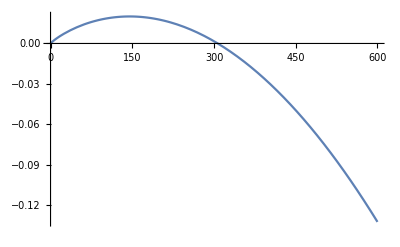

```mathematica
Plot[pseudofree[T], {T,0,600}]
```

```mathematica
WorkingPrecision
```

WorkingPrecision

```mathematica
lmin=-40;
lmax=5000;

ndiv=20;
divis = (lmax-lmin)/ndiv;
```

```mathematica
skele[tempe_]:=Table[lmin+divis*i+divis*j ,{i,0,ndiv},{j,0,ndiv}];
```

```mathematica
materold[tempe_]:=Table[Quiet[(divis)*Exp[ -(1/(kb*tempe))*(0.5*V[lmin+divis*i] +0.5*V[lmin+divis*j]+W[lmin+divis*i,lmin+divis*j])] ,General::unfl] ,{i,0,ndiv},{j,0,ndiv}];
maternum[tempe_]:=Table[N[(divis)*Exp[ -(1/(kb*tempe))*(0.5*V[lmin+divis*i] +0.5*V[lmin+divis*j]+W[lmin+divis*i,lmin+divis*j])],10] ,{i,0,ndiv},{j,0,ndiv}];
mater[tempe_]:=Table[(divis)*Exp[ -(1/(kb*tempe))*(0.5*V[lmin+divis*i] +0.5*V[lmin+divis*j]+W[lmin+divis*i,lmin+divis*j])] ,{i,0,ndiv},{j,0,ndiv}];
mater2[tempe_]:=Table[(divis) ,{i,0,ndiv},{j,0,ndiv}];
```

```mathematica
materold[0.01]//MatrixForm
```

(Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[] | Underflow[]
Underflow[] | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 2.528321245706886`6.153942954179019*^-2744297102 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.88331903949616321021279279`5.8845481289815025*^-5103004512 | 1.0598865373716099`5.82849100900793*^-5806080759 | 7.736047655173110488149176`5.775833402761077*^-6554516765 | 7.323252475770126`5.726186462577581*^-7348312528 | 8.99112401342061250491036574`5.679224463214312*^-8187468049
Underflow[] | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 2.528321245706886`6.153942954179019*^-2744297102 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.88331903949616321021279279`5.8845481289815025*^-5103004512 | 1.0598865373716099`5.82849100900793*^-5806080759 | 7.736047655173110488149176`5.775833402761077*^-6554516765 | 7.323252475770126`5.726186462577581*^-7348312528
Underflow[] | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 2.528321245706886`6.153942954179019*^-2744297102 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.88331903949616321021279279`5.8845481289815025*^-5103004512 | 1.0598865373716099`5.82849100900793*^-5806080759 | 7.736047655173110488149176`5.775833402761077*^-6554516765
Underflow[] | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 2.528321245706886`6.153942954179019*^-2744297102 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.88331903949616321021279279`5.8845481289815025*^-5103004512 | 1.0598865373716099`5.82849100900793*^-5806080759
Underflow[] | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 2.528321245706886`6.153942954179019*^-2744297102 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.88331903949616321021279279`5.8845481289815025*^-5103004512
Underflow[] | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 2.528321245706886`6.153942954179019*^-2744297102 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 4.34023783182931148`5.944474175912394*^-4445288023
Underflow[] | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 2.528321245706886`6.153942954179019*^-2744297102 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291
Underflow[] | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 2.528321245706886`6.153942954179019*^-2744297102 | 5.0288435063724081335668`6.078366634979047*^-3265934318
Underflow[] | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 2.528321245706886`6.153942954179019*^-2744297102
Underflow[] | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644
Underflow[] | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 1.394233917525350731424358`6.328240824223073*^-1837101944
Underflow[] | 2.528321245706886`6.153942954179019*^-2744297102 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 1.5292359032420858909`6.430543875289462*^-1451544002
Underflow[] | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 2.528321245706886`6.153942954179019*^-2744297102 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818
Underflow[] | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 2.528321245706886`6.153942954179019*^-2744297102 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724 | 4.01353×10^-816507392
Underflow[] | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 2.528321245706886`6.153942954179019*^-2744297102 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813 | 9.60373×10^-567028724
Underflow[] | 1.88331903949616321021279279`5.8845481289815025*^-5103004512 | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 2.528321245706886`6.153942954179019*^-2744297102 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660 | 2.980426×10^-362909813
Underflow[] | 1.0598865373716099`5.82849100900793*^-5806080759 | 1.88331903949616321021279279`5.8845481289815025*^-5103004512 | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 2.528321245706886`6.153942954179019*^-2744297102 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266 | 1.199614×10^-204150660
Underflow[] | 7.736047655173110488149176`5.775833402761077*^-6554516765 | 1.0598865373716099`5.82849100900793*^-5806080759 | 1.88331903949616321021279279`5.8845481289815025*^-5103004512 | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 2.528321245706886`6.153942954179019*^-2744297102 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629 | 6.262234×10^-90751266
Underflow[] | 7.323252475770126`5.726186462577581*^-7348312528 | 7.736047655173110488149176`5.775833402761077*^-6554516765 | 1.0598865373716099`5.82849100900793*^-5806080759 | 1.88331903949616321021279279`5.8845481289815025*^-5103004512 | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 2.528321245706886`6.153942954179019*^-2744297102 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750 | 4.2397672×10^-22711629
Underflow[] | 8.99112401342061250491036574`5.679224463214312*^-8187468049 | 7.323252475770126`5.726186462577581*^-7348312528 | 7.736047655173110488149176`5.775833402761077*^-6554516765 | 1.0598865373716099`5.82849100900793*^-5806080759 | 1.88331903949616321021279279`5.8845481289815025*^-5103004512 | 4.34023783182931148`5.944474175912394*^-4445288023 | 1.2972637109593173519786543384`6.0088430470566925*^-3832931291 | 5.0288435063724081335668`6.078366634979047*^-3265934318 | 2.528321245706886`6.153942954179019*^-2744297102 | 1.64862354261830566111037900173`6.236727269281045*^-2268019644 | 1.394233917525350731424358`6.328240824223073*^-1837101944 | 1.5292359032420858909`6.430543875289462*^-1451544002 | 2.1753955257935439231470316037427278`6.54652486109621*^-1111345818 | 4.01353×10^-816507392 | 9.60373×10^-567028724 | 2.980426×10^-362909813 | 1.199614×10^-204150660 | 6.262234×10^-90751266 | 4.2397672×10^-22711629 | 3.7228847181×10^-31750)

```mathematica
Max@Eigenvalues[materold];
```

```mathematica
-((kb*0.01))*Log[Max@Eigenvalues[mat]];
```

```mathematica
freienergie[temp_]:=-((kb*temp))*Log[Max@Eigenvalues[materold[temp]]]
```

```mathematica
Plot[freienergie[tem],{tem,0.1,100}, PlotPoints->50]
```

Eigenvalues::unfl: Underflow occurred in computation.

General::stop: Further output of Eigenvalues::unfl will be suppressed during this calculation.

-Graphics-

```mathematica
mater[0.01];
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

```mathematica
-((kb*10^-5))*Log[Max@Eigenvalues[mater[10^-5]]]//TraditionalForm;
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

Eigenvalues::unfl: Underflow occurred in computation.

```mathematica
Max@Eigenvalues@mater[10^-5];
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

Eigenvalues::unfl: Underflow occurred in computation.

```mathematica
Max@Eigenvalues@mater2[10^-5]//N
```

5292.

```mathematica
test[f_,i_,j_]:=Exp[ -(1/(kb*f))*(0.5*V[lmin+divis*i] +0.5*V[lmin+divis*j]+W[lmin+divis*i,lmin+divis*j])]
```

```mathematica
test[10^-5,0,0]
```

General::unfl: Underflow occurred in computation.

Underflow[]

```mathematica
Exp[-1/10^-5]//N
```

3.562949565×10^-43430

```mathematica
test3[i_,j_]:=(0.5*V[lmin+divis*i] +0.5*V[lmin+divis*j]+W[lmin+divis*i,lmin+divis*j])
```

```mathematica
test3[0,0]
```

3.49059×10^33

```mathematica
RM=RandomReal[1,{5,5}];
SM=UpperTriangularize[RM]+Transpose[UpperTriangularize[RM,1]]
```

{{0.446583,0.731747,0.939196,0.0150694,0.253776},{0.731747,0.505788,0.0462638,0.795758,0.119027},{0.939196,0.0462638,0.743197,0.425939,0.139366},{0.0150694,0.795758,0.425939,0.277683,0.709332},{0.253776,0.119027,0.139366,0.709332,0.564257}}

```mathematica
SM//MatrixForm
```

Transpose[UpperTriangularize[RandomReal[K,{5,5}],1]]+UpperTriangularize[RandomReal[K,{5,5}]]

```mathematica
Eigenvalues@SM
```

Eigenvalues[Transpose[UpperTriangularize[RandomReal[K,{5,5}],1]]+UpperTriangularize[RandomReal[K,{5,5}]]]

```mathematica
Max@Eigenvalues[Exp[-1/0.00001]*SM]
```

Eigenvalues[3.562949565×10^-43430 (Transpose[UpperTriangularize[RandomReal[K,{5,5}],1]]+UpperTriangularize[RandomReal[K,{5,5}]])]

```mathematica
V[-200]
```

3.28953×10^172

```mathematica
Exp[-V[-40]]
```

General::unfl: Underflow occurred in computation.

Underflow[]

```mathematica
Quiet[Exp[-V[-40]],General::munfl]
```

General::unfl: Underflow occurred in computation.

Underflow[]

```mathematica
Activate@SetPrecision[Inactivate[Exp[-V[-40]]],15]
```

General::unfl: Underflow occurred in computation.

Underflow[]

```mathematica
c1=N[Exp[700]]
c2=N[Exp[-380]]
```

1.01423×10^304

9.29174×10^-166

```mathematica
c1 c2^2
```

8.75651×10^-27

```mathematica
Log[Exp[SetPrecision[-V[-40],10]]]
```

General::unfl: Underflow occurred in computation.

Underflow[]

```mathematica
Ising[beta_,J_,h_]:=Exp[beta*J]*Cosh[beta*h]+Sqrt[Exp[2*beta*J]*(Sinh[beta*h])^2+Exp[-2*beta*J]]
```

```mathematica
Limit[-(1/beta)*Log[ Ising[beta,1,1]], beta->Infinity]
```

-2

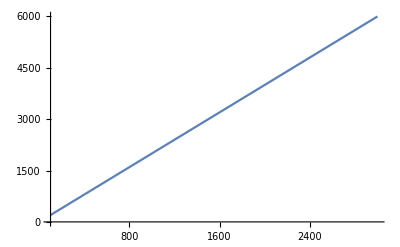

```mathematica
Plot[Log[ Ising[beta,1,1]],{beta,100,3000}]
```

```mathematica
cold[beta_,J_,h_]:=-(1/beta)*Log[ Ising[beta,J,h]]
```

```mathematica
cold[100000,1,1]//N
```

-2.

```mathematica
Eigenvalues[SM]
```

{2.20482,-1.04136,0.934462,0.501772,-0.0621854}

{-1.04136,-0.0621854,0.501772,0.934462,2.20482}

```mathematica
Eigenvalues[3*SM]
```

{6.61445,-3.12407,2.80339,1.50532,-0.186556}

```mathematica
Eigenvalues[3*SM]==3*Eigenvalues[SM]
```

True

```mathematica
A={{1,2},{2,5}}
```

{{1,2},{2,5}}

```mathematica
A//MatrixForm
```

(1 | 2
2 | 5)

```mathematica
A^2
```

{{1,4},{4,25}}

```mathematica
Eigenvalues[A^2]
```

{13+4 √10,13-4 √10}

```mathematica
Eigenvalues [A]
```

{5,1}

```mathematica
eigpower[T_]:=Log[ Max@Eigenvalues[A^(1/T)]]
eigpowerapp[T_]:=(1/T)*Log[Max@Eigenvalues@A]
```

```mathematica
eigpower[1]
```

Log[4]

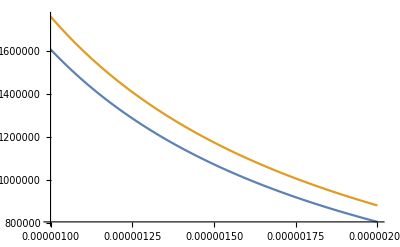

```mathematica
Plot[{eigpower[T],eigpowerapp[T]},{T,1*^-6,2*^-6}]
```